```mathematica
Get["ArduinoHelpers.wl", Path->"/home/teemu/Documents/Projects/Mathematica/"]
```

```mathematica
?ArduinoHelpers`*
```

```mathematica
arduino=OpenArduinoSerial[DefaultSerialPort]
```

DeviceObject[…]

```mathematica
SynchronizeTime[arduino]
```

True

```mathematica
temperatureTrend=ReadTemperatureTrend[arduino]
```

TimeSeries[…]

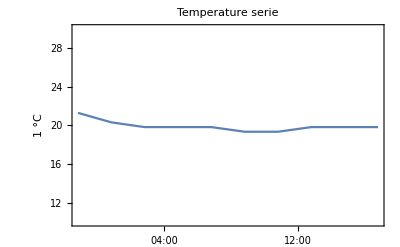

```mathematica
DateListPlot[temperatureTrend,{PlotRange->{Automatic,{10.0,+30.0}},PlotLabel->"Temperature serie",AxesLabel->Quantity[, "DegreesCelsiusDifference"]}]
```

```mathematica
CloseArduinoSerial[arduino];
```